“Anarchy” diagram

```mathematica
ClearAll;
AA={{t21^-1+(t32+t21)^-1,(t32+t21)^-1},{(t32+t21)^-1,t32^-1+(t32+t21)^-1}};iAA=Simplify[Inverse[AA]];
(*Print["A = ",AA//MatrixForm,"  A^-1 = ",iAA//MatrixForm,"  Det(A) = ",Simplify[Det[AA]]//MatrixForm];*)
A3=KroneckerProduct[AA,IdentityMatrix[3]];
iA3=Simplify[Inverse[A3]];
Print["A_(3  D) = ",A3//MatrixForm,"  Det(A_(3  D)) = ",Simplify[Det[A3]]//MatrixForm];
Print[Simplify[(((t32+t21) t21 t32)^3 Det[A3])^(-1/2)]];
```

A_(3  D) = (1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0 | 0
0 | 1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0
0 | 0 | 1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32)
1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32) | 0 | 0
0 | 1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32) | 0
0 | 0 | 1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32))  Det(A_(3  D)) = 8/(t21^3 t32^3)

1/(2 √2 √((t21+t32)^3))

“Fish-slash” diagram

```mathematica
ClearAll;
AA={{t21^-1+(t32+t21)^-1,(t32+t21)^-1,0},{(t32+t21)^-1,t32^-1+(t32+t21)^-1+(t43+t32)^-1,(t43+t32)^-1},{0,(t43+t32)^-1,(t43+t32)^-1+t43^-1}};iAA=Simplify[Inverse[AA]];
(*Print["A = ",AA//MatrixForm,"  A^-1 = ",iAA//MatrixForm,"  Det(A) = ",Simplify[Det[AA]]//MatrixForm];*)
A3=KroneckerProduct[AA,IdentityMatrix[3]];
iA3=Simplify[Inverse[A3]];
Print["A_(3  D) = ",A3//MatrixForm,"  Det(A_(3  D)) = ",Simplify[Det[A3]]//MatrixForm];
Print[Simplify[(((t32+t21) t21 t32 t43(t43+t32))^3 Det[A3])^(-1/2)]];
```

A_(3  D) = (1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0 | 0 | 0 | 0 | 0
0 | 1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0 | 0 | 0 | 0
0 | 0 | 1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0 | 0 | 0
1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32)+1/(t32+t43) | 0 | 0 | 1/(t32+t43) | 0 | 0
0 | 1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32)+1/(t32+t43) | 0 | 0 | 1/(t32+t43) | 0
0 | 0 | 1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32)+1/(t32+t43) | 0 | 0 | 1/(t32+t43)
0 | 0 | 0 | 1/(t32+t43) | 0 | 0 | 1/t43+1/(t32+t43) | 0 | 0
0 | 0 | 0 | 0 | 1/(t32+t43) | 0 | 0 | 1/t43+1/(t32+t43) | 0
0 | 0 | 0 | 0 | 0 | 1/(t32+t43) | 0 | 0 | 1/t43+1/(t32+t43))  Det(A_(3  D)) = (4 t21 (t32+t43)+t32 (3 t32+4 t43))^3/(t21^3 t32^3 (t21+t32)^3 t43^3 (t32+t43)^3)

1/(√((4 t21 (t32+t43)+t32 (3 t32+4 t43))^3))

“Gauss-Fish” diagram

```mathematica
ClearAll;
AA={{t21^-1+(t32+t21)^-1,(t32+t21)^-1,0,0,0},{(t32+t21)^-1,t32^-1+(t32+t21)^-1+(t54+t43+t32)^-1,(t54+t43+t32)^-1,(t54+t43+t32)^-1,0},{0,(t54+t43+t32)^-1,(t54+t43+t32)^-1+t43^-1+t43^-1,(t54+t43+t32)^-1,0},{0,(t54+t43+t32)^-1,(t54+t43+t32)^-1,(t54+t43+t32)^-1+(t65+t54)^-1+t54^-1,(t65+t54)^-1},{0,0,0,(t65+t54)^-1,(t65+t54)^-1+t65^-1}};iAA=Simplify[Inverse[AA]];
(*Print["A = ",AA//MatrixForm,"  A^-1 = ",iAA//MatrixForm,"  Det(A) = ",Simplify[Det[AA]]//MatrixForm];*)
A3=KroneckerProduct[AA,IdentityMatrix[3]];
iA3=Simplify[Inverse[A3]];
Print["A_(3  D) = ",A3//MatrixForm,"  Det(A_(3  D)) = ",Simplify[Det[A3]]//MatrixForm];
Print[Simplify[(((t32+t21) t21 t32 t43 t43 t54 t65(t54+t43+t32) (t65+t54))^3 Det[A3])^(-1/2)]];
```

A_(3  D) = (1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32)+1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 0 | 0 | 0
0 | 1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32)+1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 0 | 0
0 | 0 | 1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32)+1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 0
0 | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 2/t43+1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 2/t43+1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 2/t43+1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 0
0 | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/t54+1/(t32+t43+t54)+1/(t54+t65) | 0 | 0 | 1/(t54+t65) | 0 | 0
0 | 0 | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/t54+1/(t32+t43+t54)+1/(t54+t65) | 0 | 0 | 1/(t54+t65) | 0
0 | 0 | 0 | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/t54+1/(t32+t43+t54)+1/(t54+t65) | 0 | 0 | 1/(t54+t65)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(t54+t65) | 0 | 0 | 1/t65+1/(t54+t65) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(t54+t65) | 0 | 0 | 1/t65+1/(t54+t65) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(t54+t65) | 0 | 0 | 1/t65+1/(t54+t65))  Det(A_(3  D)) = (64 (t32 (3 t32 (t54+t65)+3 t43 (t54+t65)+t54 (3 t54+4 t65))+t21 (4 t32 (t54+t65)+3 t43 (t54+t65)+t54 (3 t54+4 t65)))^3)/(t21^3 t32^3 (t21+t32)^3 t43^3 t54^3 (t32+t43+t54)^3 t65^3 (t54+t65)^3)

1/(8 √(t43^3 (t32 (3 t32 (t54+t65)+3 t43 (t54+t65)+t54 (3 t54+4 t65))+t21 (4 t32 (t54+t65)+3 t43 (t54+t65)+t54 (3 t54+4 t65)))^3))

```mathematica
Amat={{1,0,0},{0,1,0},{0,0,1}};Print["A = ",Amat//MatrixForm,"   A^-1 = ",Simplify[Inverse[Amat]]//MatrixForm,"   Det(A) = ",Simplify[Det[Amat]]//MatrixForm];
Simplify[(Inverse[Amat][[1,1]] Inverse[Amat][[2,2]] Inverse[Amat][[3,3]]+Inverse[Amat][[1,2]] Inverse[Amat][[2,1]] Inverse[Amat][[3,3]]+Inverse[Amat][[1,1]] Inverse[Amat][[2,3]] Inverse[Amat][[3,2]]+Inverse[Amat][[1,3]] Inverse[Amat][[2,2]] Inverse[Amat][[3,1]]+Inverse[Amat][[1,2]] Inverse[Amat][[2,3]] Inverse[Amat][[3,1]]) ((2 π)^(3/2)/√Det[Amat])]
Integrate[x^2 y^2 z^2 Exp[-1/2(Expand[{x,y,z}.Amat.{x,y,z}])],{x,0,Infinity},{y,0,Infinity},{z,0,Infinity}]
```

A = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)   A^-1 = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)   Det(A) = 1

2 √2 π^(3/2)

π^(3/2)/(2 √2)

```mathematica
spacedim=1;
ami=KroneckerProduct[{{a,-a},{-a,a}},IdentityMatrix[spacedim]];
ami//MatrixForm
```

(a | -a
-a | a)

```mathematica
Sum[q^n p^m,{n,0,Infinity},{m,0,Infinity},Assumptions->{q<1,p<1}]
```

1/((1-p) (1-q))

```mathematica
bsu[ϵ_,E_]:=Integrate[t^(-3/2) Exp[-t E],{t,ϵ,Infinity},Assumptions->{ϵ>0,E>0}];
bsu[λ,ee]
Integrate[t^(-3/2) Exp[-t ee],t,Assumptions->ee>0]
```

(2 ⅇ^(-ee λ))/(√λ)-2 √ee √π Erfc[√(ee λ)]

-(2 ⅇ^(-ee t))/(√t)+(2 √(ee t) Gamma[1/2,ee t])/(√t)

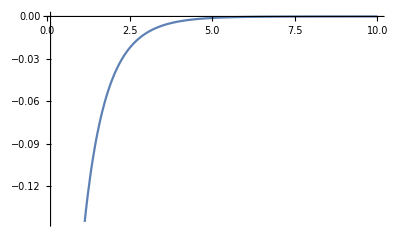

```mathematica
t=1;
Plot[-(2/(E^(EE*t)*Sqrt[t])) + (2*Sqrt[EE*t]*Gamma[1/2, EE*t])/Sqrt[t],{EE,0.1,10},PlotPoints->10]
```

Power::infy: Infinite expression 1/0. encountered.

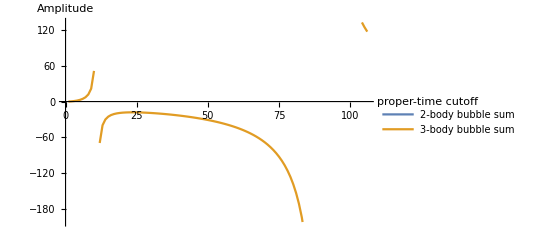

```mathematica
a=2;
tr=Range[0,10.5,0.1];
bub2=C Sum[(C/(√ϵ))^n,{n,0,Infinity}]/.{ϵ->tr,C->1/(a+ϵ^(-1/2))};
bub3=C^2 Sum[(3^(n+2)-3) (C/(√ϵ))^n,{n,0,Infinity}]/.{C->1,ϵ->tr};
ListPlot[{bub2,bub3},Joined->True,PlotLegends->{"2-body bubble sum","3-body bubble sum"},AxesLabel->{"proper-time cutoff","Amplitude"}]
```

```mathematica
al=as;
renbub2=Simplify[I C Sum[((I C)/(√ϵ))^n,{n,0,Infinity}]/.{C->1/(al+ϵ^(-1/2))}]
renbub3=Simplify[C^2 Sum[(3^(n+2)-3) ((I C)/(√ϵ))^n,{n,0,Infinity}]/.{C->1/(al+ϵ^(-1/2))}]
(*ListPlot[{Transpose[{tr,Table[renbub2,{ϵ,tr}]}],Transpose[{tr,renbub3/.ϵ->tr}]},Joined->True,PlotLegends->{"2-body bubble sum","3-body bubble sum"},AxesLabel->{"proper-time cutoff","Amplitude"}]*)
```

(ⅈ √ϵ)/((1-ⅈ)+as √ϵ)

(6 ϵ)/((-2-4 ⅈ)+(2-4 ⅈ) as √ϵ+as^2 ϵ)

```mathematica
sols=Solve[3 ϵ^-1-4 C^-1 ϵ^(-1/2)+C^-2-6 a3==0,C]
```

{{C→(-2 √ϵ-√(ϵ+6 a3 ϵ^2))/(3 (-1+2 a3 ϵ))},{C→(-2 √ϵ+√(ϵ+6 a3 ϵ^2))/(3 (-1+2 a3 ϵ))}}

{(2 ϵ+√ϵ √(ϵ (1+18 ϵ)))/(√ϵ-18 ϵ^(3/2)-√(ϵ (1+18 ϵ))),(2 ϵ-√ϵ √(ϵ (1+18 ϵ)))/(√ϵ-18 ϵ^(3/2)+√(ϵ (1+18 ϵ)))}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

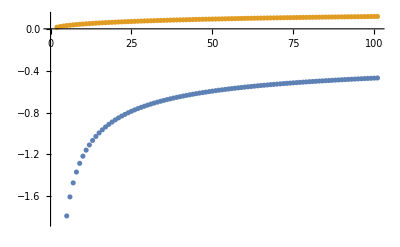

```mathematica
a3=3;
tmp2=Simplify[C Sum[(C/(√ϵ))^n,{n,0,Infinity}]/.sols]
ListPlot[tmp2/.ϵ->tr]
```

```mathematica
amat={{a+b+2 c,-2 c},{-2 c,d+e+2 c}};svec={x1 a+x2 b,x3 e+x4 d};
amat//MatrixForm
svec//MatrixForm
```

(a+b+2 c | -2 c
-2 c | 2 c+d+e)

(a x1+b x2
e x3+d x4)

```mathematica
Simplify[svec.Inverse[amat].svec]//MatrixForm
```

(a^2 (2 c+d+e) x1^2+2 a b (2 c+d+e) x1 x2+b^2 (2 c+d+e) x2^2+2 c (e x3+d x4)^2+a (e x3+d x4) (4 c x1+e x3+d x4)+b (e x3+d x4) (4 c x2+e x3+d x4))/(2 c (d+e)+a (2 c+d+e)+b (2 c+d+e))

```mathematica
Det[amat]
```

2 a c+2 b c+a d+b d+2 c d+a e+b e+2 c e